-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 6 II.D Many Random Variables

```mathematica
(*-------------------------------------*)
t1=TimeObject[{7,0,0}];
t2=TimeObject[{7,10,0}];
Lab1="Thermo.&Stat.\nGeneral Picture";
(*-------------------------------------*)
(*-------------------------------------*)
t3=TimeObject[{7,8,0}];
t4=TimeObject[{7,30,0}];
Lab2="Thermo.&Stat.\nMindMap Lecture";
(*-------------------------------------*)
(*-------------------------------------*)
t5=TimeObject[{8,2,0}];
t6=TimeObject[{8,20,0}];
Lab3="Thermo.&Stat.\nStudents talks";
(*-------------------------------------*)
(*-------------------------------------*)
t71=TimeObject[{8,5,0}];
t81=TimeObject[{8,10,0}];
Lab41="Thermo.&Stat.\nBreak";
(*-------------------------------------*)
(*-------------------------------------*)
t7=TimeObject[{7,35,0}];
t8=TimeObject[{8,45,0}];
Lab4="Thermo.&Stat.\nSlides";
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
t72=TimeObject[{8,50,0}];
t82=TimeObject[{9,0,0}];
Lab42=Hyperlink[Style["Thermo.&Stat.\n   Questions?\n   &\n   Chat..."],"https://mmaitex-gemmini.fly.dev/"];

TS1=TimelinePlot[{
Interval[{t1,t2}]->Lab1,
Interval[{t3,t4}]->Lab2,
Interval[{t5,t6}]->Lab3,
Interval[{t71,t81}]->Lab41,
Interval[{t7,t8}]->Lab4,
Interval[{t72,t82}]->Lab42
},
Frame->True,
FrameStyle->Directive[Thickness[0.003],FontFamily->"Comic Sans MS", FontSize->28],
LabelStyle->Directive[FontFamily->"Comic Sans MS",Black,18],ImageSize->800,Background->LightBlue,AspectRatio->0.35
]
```

-Graphics-

## What we need to know:

### Gaussian distribution 1D:

(ⅇ^(-x^2/2))/(√(2 π))

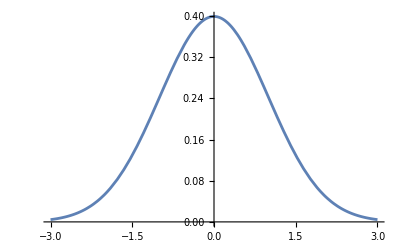

```mathematica
myPDF=PDF[NormalDistribution[0,1],x]
Plot[myPDF,{x,-3,3}]
```

```mathematica
myProba=Integrate[myPDF,{x,0.5,1.0}]
```

0.149882

#### The mean for a gaussian:

```mathematica
myFave=⟨f[x]⟩==Integrate[TraditionalForm[(myPDF)]*f[x],{x,-∞,+∞}];
Framed[MaTeX[myFave,Magnification->5]]
```

-Graphics-

#### In General 1D:

-Graphics-

#### In General 1D:

```mathematica
myFave=⟨f[x]⟩==Integrate[HoldForm[ρ[x]*f[x]],{x,-∞,+∞}];
Framed[MaTeX[myFave,Magnification->5]]
myFave=⟨f[x]⟩==IntegralOperator[x][HoldForm[ρ[x]*f[x]]];
Framed[MaTeX[myFave,Magnification->5]]
```

-Graphics-

-Graphics-

### Derivatives

```mathematica
Clear[f,x];
f=1/x;
r=DifferentialOperator[x][f]==pdConv[D[f,x]];
MaTeX[r,Magnification->3]
```

-Graphics-

```mathematica
Clear[f,x];
f=Log[x];
r=DifferentialOperator[x][f]==pdConv[D[f,x]];
MaTeX[r,Magnification->3]
```

-Graphics-

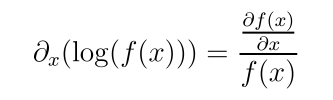

```mathematica
Clear[f,x];
f1=Log[f[x]];
r=DifferentialOperator[x][f1]==pdConv[D[f1,x]];
MaTeX[r,Magnification->3]
```

### Integrals:

```mathematica
Clear[f,x];
f1=1/x;
r=IntegralOperator[x][f1]==Integrate[f1,x];
MaTeX[r,Magnification->3]
```

-Graphics-

### Exponentials

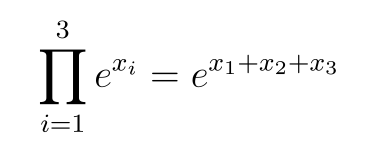

```mathematica
Clear[f,x];
Nvars=3;
f1=∏_(i=1)^Nvars Power[ⅇ,Subscript[x, i]];
r=HoldForm[∏_(i=1)^3 Power[ⅇ,Subscript[x, i]]]==f1;
MaTeX[r,Magnification->4]
```

### Logarithms

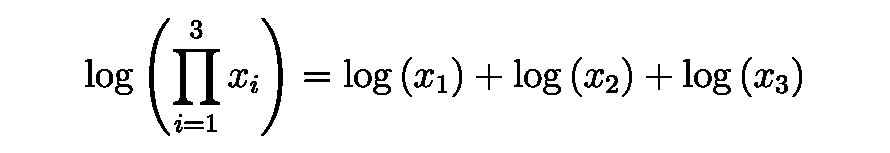

```mathematica
Clear[f1];
Nvars=3;
f1=∑_(i=1)^Nvars Log[Subscript[x, i]];
r=Log[HoldForm[∏_(i=1)^3 Subscript[x, i]]]==f1;
MaTeX[r,Magnification->4]
```

## Functions

```mathematica
(* ====================================================*)
(* == Para Integrales bonitas == *)
IntegralOperator/:MakeBoxes[IntegralOperator[x__],form_]:=With[{sub=RowBox@BoxForm`MakeInfixForm[{x},",",form]},InterpretationBox[SubscriptBox["∫ⅆx",""],IntegralOperator[x]]]
(* ====================================================*)
(* ====================================================*)
(* === Para escribir derivadas muy bonitas ==*)
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
(* == Para derivadas bonitas == *)
DifferentialOperator/:MakeBoxes[DifferentialOperator[x__],form_]:=With[{sub=RowBox@BoxForm`MakeInfixForm[{x},",",form]},InterpretationBox[SubscriptBox["∂",sub],DifferentialOperator[x]]]
(* ====================================================*)
```

```mathematica
(1) -- Today, we're going to talk about something called "random variables" and how we can describe them.

Imagine you're playing a game where you have to guess the position and speed of a tiny particle in the air, like a speck of dust or a tiny bug. To do that, you need to know six different numbers or "coordinates." These coordinates tell you where the particle is and how fast it's moving.

Now, let's say you have more than one particle to keep track of. Each particle will have its own set of six coordinates. So, if you have two particles, you'll need twelve coordinates in total. If you have three particles, you'll need eighteen coordinates, and so on.

All of these coordinates together form what we call an "N-dimensional space." The letter "N" stands for the number of particles you're dealing with. The more particles you have, the more dimensions you need to describe their positions and speeds.

It's like having a big, multi-dimensional game board where each particle is represented by a set of coordinates. And just like in a game, you need to know all these coordinates to keep track of what's going on!
```

## The joint PDF p(x)

```mathematica
(2) --
 The joint $PDF p(\mathbf{x})$, is the probability density of an outcome in a volume element $d^{N} \mathbf{x}=\prod_{i=1}^{N} d x_{i}$ around the point $\mathbf{x}=\left\{x_{1}, x_{2}, \cdots, x_{N}\right\}$. The joint PDF is normalized such that


(2) -- Imagine a bunch of little toys, like cars or dolls, scattered around a room. The room is like a big box, and each toy is a little dot inside that box. Now, let's think about the chances of finding a toy in a particular spot in the room.

The room is divided into tiny, tiny sections, and we want to know how likely it is to find a toy in one of those tiny sections. That's what the joint PDF (p(x)) tells us. It's like a special way of counting how many toys might be in each tiny section.

To make sure we're counting correctly, we have a rule: if we add up all the chances of finding a toy in every single tiny section of the room, the total should be exactly 1. That means we're not missing any toys or double-counting them.

So, when you see the joint PDF (p(x)), it's like a secret code that tells us how likely we are to find our toys in different parts of the room. And the rule about adding up to 1 makes sure we're not losing track of any toys!
```

Statistical Mechanics
Ramirez (3)

```mathematica
MaTeX["p_{\\mathbf{x}}(\\mathcal{S})=\\int p(\\mathbf{x}) \\,  d^N\\mathbf{x}=1", Magnification -> 4]
```

-Graphics-

```mathematica
(4) -- If, and only if, the N random variables are independent, the joint PDF is the product of individual PDFs,
```

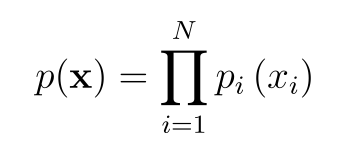

```mathematica
MaTeX["p(\\mathbf{x})=\\prod_{i=1}^{N} p_{i}\\left(x_{i}\\right)", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["p(\\mathbf{x})=\\prod_{i=1}^{N} p_{i}\\left(x_{i}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[x]==∏_(i=1)^N p_i[x_i]

Statistical Mechanics
Ramirez (5)

## The unconditional PDF

```mathematica
(6) -- The unconditional PDF describes the behavior of a subset of random variables, independent of the values of the others. For example, if we are interested only in the location of a gas particle, an unconditional PDF can be constructed by integrating over all velocities at a given location,
```

```mathematica
MaTeX["p(\vec{x})=\int d^{3}\vec{v} p(\vec{x}, \vec{v})", Magnification->4]
```

-Graphics-

more generally ==>

Statistical Mechanics
Ramirez (7)

```mathematica
MaTeX["p\\left(x_{1}, \\cdots, x_{m}\\right)=\\int \\prod_{i=m+1}^{N} d x_{i} p\\left(x_{1}, \\cdots, x_{N}\\right)", Magnification -> 4]
```

-Graphics-

## The conditional PDF

```mathematica
(8) --  The conditional PDF describes the behavior of a subset of random variables, for specified values of the others. For example, the PDF for the velocity of a particle at a particular location $\vec{x}$, denoted by $p(\vec{v} \mid \vec{x})$, is proportional to the joint PDF $p(\vec{v} \mid \vec{x})=p(\vec{x}, \vec{v}) / \mathcal{N}$. The constant of proportionality, obtained by normalizing $p(\vec{v} \mid \vec{x})$, is


(8) -- Have you ever played with toy cars or balls? Well, imagine one of those toys moving around. The way it moves and the direction it goes is like a secret code that we call the "conditional PDF." This code tells us how the toy might move if it's in a certain place.

For example, if your toy car is at a particular spot (let's call it x), the code (which we write as p(v|x)) tells us how fast and in what direction the car might go. It's like a special instruction book for that particular place.

This code is related to another code called the "joint PDF," which we write as p(x, v). The joint PDF is like a bigger instruction book that tells us how the toy might move in any place. The conditional PDF is just a small part of that bigger book, but it's very important because it helps us understand how the toy behaves in a specific spot.

To get the conditional PDF from the joint PDF, we need to do a little bit of math. We divide the joint PDF by a special number called the "constant of proportionality." This number makes sure that the conditional PDF is correct and follows all the rules of how toys should move.

So, in simple terms, the conditional PDF is like a secret code that tells us how a toy might move in a particular place, and it's related to a bigger code called the joint PDF. It's like having a special instruction book just for that one spot, which helps us understand how the toy behaves there.
```

Statistical Mechanics
Ramirez (9)

```mathematica
MaTeX["\\mathcal{N}=\\int p(\\vec{x}, \\vec{v}) \\,  d \\vec{v} =p(\\vec{x})", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{(Nnum)}=\\int p(\\vec{x}, \\vec{v}) \\,  d \\vec{v} =p(\\vec{x})",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Nnum==∫p[x⃗,v⃗]ⅆ v⃗==p[x⃗]

```mathematica
(10) -- the unconditional PDF for a particle at x. In general, the unconditional PDFs are obtained from Bayes' Theorem as
```

Statistical Mechanics
Ramirez (11)

## Bayes’ Theorem

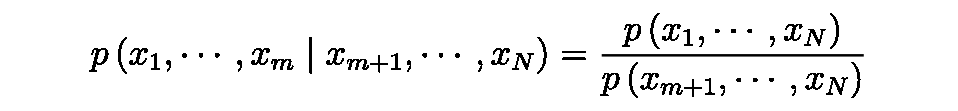

```mathematica
MaTeX["p\\left(x_{1}, \\cdots, x_{m} \\mid x_{m+1}, \\cdots, x_{N}\\right)=\\frac{p\\left(x_{1}, \\cdots, x_{N}\\right)}{p\\left(x_{m+1}, \\cdots, x_{N}\\right)}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["p\\left(x_{1}, \\cdots, x_{m} \\mid x_{m+1}, \\cdots, x_{N}\\right)=\\frac{p\\left(x_{1}, \\cdots, x_{N}\\right)}{p\\left(x_{m+1}, \\cdots, x_{N}\\right)}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[x_1,⋯,x_m|x_(m+1),⋯,x_N]==p[x_1,⋯,x_N]/p[x_(m+1),⋯,x_N]

(12) -- Note that if the random variables are independent, the unconditional PDF is equal to the conditional PDF.

(12) -- Imagine you have a big box filled with toys. Some toys are red, some are blue, and some are green. The red toys are cars, the blue toys are balls, and the green toys are blocks.

Now, let's say you want to pick a toy from the box without looking. You can pick any toy, no matter what color or shape it is. That's like having a random variable, where you don't know what you'll get.

But what if you already know that you picked a red toy? Then, the only toys you can pick are cars. This is like a conditional random variable, where you know something about the toy before you pick it.

Here's the special part: if the toys in the box are all mixed up and don't depend on each other, then the chances of picking any toy from the whole box are the same as the chances of picking a car from the red toys. In other words, the unconditional PDF (the chances of picking any toy) is equal to the conditional PDF (the chances of picking a car, given that you already know it's red).

Isn't that amazing? Even though you know something about the toy before you pick it, the chances of picking it are still the same as if you didn't know anything at all! But this only works if the toys are independent, meaning the color and shape don't depend on each other.

## Break or new notes...

Statistical Mechanics
Ramirez (14)

## The expectation value of a function

```mathematica
(13) -- The expectation value of a function F(x), is obtained as before from
```

```mathematica
MaTeX["\\langle F(\\mathbf{x})\\rangle=\\int d^N \\mathbf{x} p(\\mathbf{x}) F(\\mathbf{x})", Magnification -> 4]
```

-Graphics-

## The joint characteristic function

(15) --  The joint characteristic function, is obtained from the N-dimensional Fourier transformation of the joint PDF,

(15) -- A group of tiny particles is called  N-particles. They are always moving and dancing around in their own special way. But sometimes, the scientists wanted to understand how they were moving and where they were going. 

To do this, they used a special tool called the joint characteristic function. This function was like a magic wand that could tell them all about the movements and positions of the N-particles. It was created by taking the N-dimensional Fourier transformation of the joint PDF, which was a special map that showed where all the particles were at any given time.

With the joint characteristic function, the scientists could see the patterns and rhythms of the particles' dance, and they could learn so much about their tiny world.

Statistical Mechanics
Ramirez (16)

```mathematica
MaTeX["\\tilde{p}(\\mathbf{k})=\\left\\langle\\exp \\left(-i \\sum_{j=1}^{N} k_{j} x_{j}\\right)\\right\\rangle", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\tilde{p}(\\mathbf{k})=\\left\\langle\\exp \\left(-i \\sum_{j=1}^{N} k_{j} x_{j}\\right)\\right\\rangle",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p̃[k]==⟨ⅇ^(-i ∑_(j=1)^N k_j x_j)⟩

```mathematica
(17) -- The joint moments and joint cumulants are generated by $\tilde{p}(\mathbf{k})$ and $\ln \tilde{p}(\mathbf{k})$ respectively, as
```

Statistical Mechanics
Ramirez (18)

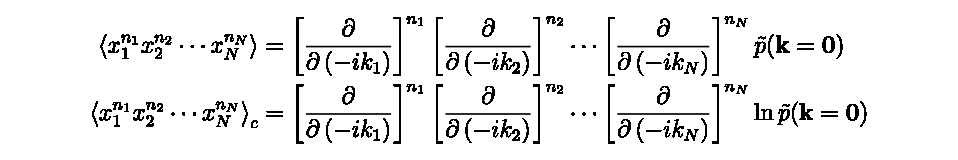

```mathematica
MaTeX["\\begin{aligned}\\left\\langle x_{1}^{n_{1}} x_{2}^{n_{2}} \\cdots x_{N}^{n_{N}}\\right\\rangle & =\\left[\\frac{\\partial}{\\partial\\left(-i k_{1}\\right)}\\right]^{n_{1}}\\left[\\frac{\\partial}{\\partial\\left(-i k_{2}\\right)}\\right]^{n_{2}} \\cdots\\left[\\frac{\\partial}{\\partial\\left(-i k_{N}\\right)}\\right]^{n_{N}} \\tilde{p}(\\mathbf{k}=\\mathbf{0}) \\\\\\left\\langle x_{1}^{n_{1}} x_{2}^{n_{2}} \\cdots x_{N}^{n_{N}}\\right\\rangle_{c} & =\\left[\\frac{\\partial}{\\partial\\left(-i k_{1}\\right)}\\right]^{n_{1}}\\left[\\frac{\\partial}{\\partial\\left(-i k_{2}\\right)}\\right]^{n_{2}} \\cdots\\left[\\frac{\\partial}{\\partial\\left(-i k_{N}\\right)}\\right]^{n_{N}} \\ln \\tilde{p}(\\mathbf{k}=\\mathbf{0})\\end{aligned}", Magnification -> 4]
```

(19) -- The previously described graphical relation between joint moments (all clusters of labelled points), and joint cumulant (connected clusters) is still applicable. For example

(19) -- Once upon a time, there were some little dots and lines that lived in a very special place called a graph. The dots were called "moments," and they liked to gather in groups called "clusters." Some of these clusters were connected by lines, and those special clusters were called "cumulants."

Now, the moments and cumulants had a very important relationship. Just like how you can look at the shapes of clouds and imagine different animals or objects, you could look at the patterns of dots and lines in the graph and see all sorts of interesting things.

The most important thing to remember is that the cumulants (the connected clusters) could tell you a lot about the moments (the groups of dots). It was like a secret code that only the smartest scientists and mathematicians could understand.

But here's the really cool part: no matter how many dots and lines there were, or how complicated the patterns looked, the same rules applied. It was like a universal language that everyone in the graph could understand.

Of course, there were some tricky parts too. Sometimes, you had to be really careful and only look at the most important lines and dots to understand what was going on. It was like trying to find the hidden shapes in a big, messy cloud – you had to focus and use your imagination.

But that's what made it so much fun! It was like a big puzzle that never ended, and the more you learned about the dots and lines, the more amazing things you could discover.

Statistical Mechanics
Ramirez (20)

```mathematica
MaTeX["\\begin{aligned}& \\left\\langle x_{\\alpha} x_{\\beta}\\right\\rangle=\\left\\langle x_{\\alpha}\\right\\rangle_{c}\\left\\langle x_{\\beta}\\right\\rangle_{c}+\\left\\langle x_{\\alpha} x_{\\beta}\\right\\rangle_{c} \\quad, \\quad \\text {and} \\\\& \\left\\langle x_{\\alpha}^{2} x_{\\beta}\\right\\rangle=\\left\\langle x_{\\alpha}\\right\\rangle_{c}^{2}\\left\\langle x_{\\beta}\\right\\rangle_{c}+\\left\\langle x_{\\alpha}^{2}\\right\\rangle_{c}\\left\\langle x_{\\beta}\\right\\rangle_{c}+2\\left\\langle x_{\\alpha} x_{\\beta}\\right\\rangle_{c}\\left\\langle x_{\\alpha}\\right\\rangle_{c}+\\left\\langle x_{\\alpha}^{2} x_{\\beta}\\right\\rangle_{c}\\end{aligned}", Magnification -> 4]
```

-Graphics-

```mathematica
(21) -- The connected correlation, $\left\langle x_{\alpha} x_{\beta}\right\rangle_{c}$, is zero if $x_{\alpha}$ and $x_{\beta}$ are independent random variables.

(21) -- Imagine you have two friends, Alice and Bob. They like to play games together, but sometimes they play different games. When they play different games, the way Alice plays her game doesn't affect the way Bob plays his game, and vice versa. They are independent.

Now, let's say Alice likes to throw a ball, and Bob likes to spin a top. When Alice throws her ball, it doesn't matter how Bob's top is spinning, and when Bob spins his top, it doesn't matter how Alice throws her ball. They are doing their own thing, independently.

In this case, we say that the "connected correlation" between Alice's ball throwing and Bob's top spinning is zero. It means that their actions are not related or connected to each other. They are independent random things happening at the same time.

So, when two friends are doing their own things separately, without affecting each other, the "connected correlation" between their actions is zero. It's like they are playing their own games, without caring about what the other is doing.
```

## The joint Gaussian distribution

(22) -- The joint Gaussian distribution is the generalization of eq.(II.15) to N random variables, as

Statistical Mechanics
Ramirez (23)

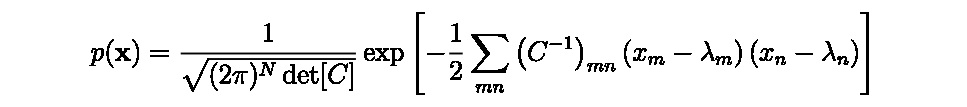

```mathematica
MaTeX["p(\\mathbf{x})=\\frac{1}{\\sqrt{(2 \\pi)^{N} \\operatorname{det}[C]}} \\exp \\left[-\\frac{1}{2} \\sum_{m n}\\left(C^{-1}\\right)_{m n}\\left(x_{m}-\\lambda_{m}\\right)\\left(x_{n}-\\lambda_{n}\\right)\\right]", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["p(\\mathbf{x})=\\frac{1}{\\sqrt{(2 \\pi)^{N} \\operatorname{det}[C]}} \\exp \\left[-\\frac{1}{2} \\sum_{m n}\\left(C^{-1}\\right)_{m n}\\left(x_{m}-\\lambda_{m}\\right)\\left(x_{n}-\\lambda_{n}\\right)\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p[x]==exp[-1/2 ∑_mn (1/C)_mn (x_m-λ_m) (x_n-λ_n)]/(√((2 π)^N det[C]))

```mathematica
(24) -- where C is a symmetric matrix, and C^{-1} is its inverse.. The simplest way to get the normalization factor is to make a linear transformation from the variables y_{j}=x_{j}-\lambda_{j}, using the unitary matrix that diagonalizes $C$. This reduces the normalization to that of the product of N Gaussians whose variances are determined by the eigenvalues of C. The product of the eigenvalues is the determinant det[C]. (This also indicates that the matrix C must be positive definite.) The corresponding joint characteristic function is obtained by similar manipulations, and is given by

(24) -- Imagine you have a bunch of little balls, and each ball has a name like x₁, x₂, x₃, and so on. These balls are all connected to each other with springs, and the springs can stretch or squish. The strength of the springs is described by a special square called C.

Now, let's say we want to know how many different ways these balls can move around while still being connected by the springs. To figure this out, we first need to find a special number called the "normalization factor."

Here's how we can do it: we can give each ball a new name, like y₁, y₂, y₃, and so on. These new names are related to the old names by subtracting a special number called λ (lambda) from each ball's old name. So, y₁ = x₁ - λ₁, y₂ = x₂ - λ₂, and so on.

When we do this, the math becomes much easier! It's like we've taken the springs and stretched or squished them in a special way so that they're all the same strength. This makes it easier to count how many different ways the balls can move.

The strength of these new, stretched or squished springs is determined by the numbers inside the square C. These numbers are called "eigenvalues," and they tell us how much each spring can stretch or squish.

To find the normalization factor, we multiply all the eigenvalues together. This gives us a special number called the "determinant," which is like a secret code that tells us everything we need to know about how the balls can move while connected by the springs.

Once we have the normalization factor, we can use it to figure out all sorts of other cool things about the balls and their springs!
```

Statistical Mechanics
Ramirez (25)

```mathematica
MaTeX["\\tilde{p}(\\mathbf{k})=\\exp \\left[-i k_{m} \\lambda_{m}-\\frac{1}{2} C_{m n} k_{m} k_{n}\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\tilde{p}(\\mathbf{k})=\\exp \\left[-i k_{m} \\lambda_{m}-\\frac{1}{2} C_{m n} k_{m} k_{n}\\right]",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

p̃[k]==exp[-i k_m λ_m-1/2 C_mn k_m k_n]

```mathematica
(26) -- where the summation convention is used.
```

(27) -- The joint cumulants of the Gaussian are then obtained from $\ln \tilde{p}(\mathbf{k})$ as

Statistical Mechanics
Ramirez (28)

```mathematica
MaTeX["\\left\\langle x_{m}\\right\\rangle_{c}=\\lambda_{m} \\quad, \\quad\\left\\langle x_{m} x_{n}\\right\\rangle_{c}=C_{m n}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace[StringSplit["\\left\\langle x_{m}\\right\\rangle_{c}=\\lambda_{m} \\quad;; \\quad\\left\\langle x_{m} x_{n}\\right\\rangle_{c}=C_{m n}", ";;"],{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

{⟨x_m⟩_c==λ_m,⟨x_m x_n⟩_c==C_mn}

```mathematica
(29) -- with all higher cumulants equal to zero. In the special case of $\left\{\lambda_{m}\right\}=0$, all odd moments of the distribution are zero, while the general rules for relating moments to cumulants indicate that any even moment is obtained by summing over all ways of grouping the involved random variables into pairs, e.g.
```

Statistical Mechanics
Ramirez (30)

```mathematica
MaTeX["\\left\\langle x_{a} x_{b} x_{c} x_{d}\\right\\rangle=C_{a b} C_{c d}+C_{a c} C_{b d}+C_{a d} C_{b c}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\left\\langle x_{a} x_{b} x_{c} x_{d}\\right\\rangle=C_{a b} C_{c d}+C_{a c} C_{b d}+C_{a d} C_{b c}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

⟨x_a x_b x_c x_d⟩==C_ab C_cd+C_ac C_bd+C_ad C_bc

```mathematica
(31) -- This result is sometimes referred to as Wick's theorem.
```

## II.E Sums of Random Variables & the Central Limit Theorem

(32) -- Consider the sum $X=\sum_{i=1}^{N} x_{i}$, where $x_{i}$ are random variables with a joint PDF of $p(\mathbf{x})$. The $\mathrm{PDF}$ for $X$ is

Statistical Mechanics
Ramirez (33)

```mathematica
MaTeX["p_{X}(x)=\\int d^{N} \\mathbf{x} p(\\mathbf{x}) \\delta\\left(x-\\sum x_{i}\\right)=\\int \\prod_{i=1}^{N-1} d x_{i} p\\left(x_{1}, \\cdots, x_{N-1}, x-x_{1} \\cdots-x_{N-1}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
(34) -- and the corresponding characteristic function (using eq.(II.38)) is given by
```

Statistical Mechanics
Ramirez (35)

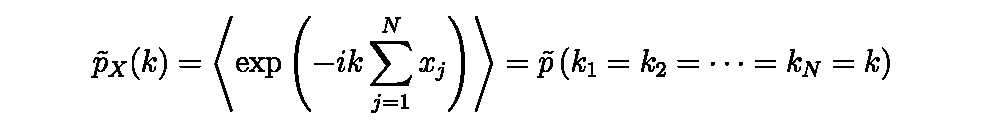

```mathematica
MaTeX["\\tilde{p}_{X}(k)=\\left\\langle\\exp \\left(-i k \\sum_{j=1}^{N} x_{j}\\right)\\right\\rangle=\\tilde{p}\\left(k_{1}=k_{2}=\\cdots=k_{N}=k\\right)", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\tilde{p}_{X}(k)=\\left\\langle\\exp \\left(-i k \\sum_{j=1}^{N} x_{j}\\right)\\right\\rangle=\\tilde{p}\\left(k_{1}=k_{2}=\\cdots=k_{N}=k\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(p̃)_X[k]==⟨ⅇ^(-i k ∑_(j=1)^N x_j)⟩==p̃[k_1==k_2==⋯==k_N==k]

```mathematica
(36) -- Cumulants of the sum are obtained by expanding $\ln \tilde{p}_{X}(k)$,

(36) -- Thermodynamics is all about understanding how things work when they become hot or cold. It's like when you bake cookies in the oven, or when you put ice cream in the freezer. We can use special math tricks to figure out how things change when we add or remove heat.

One of these math tricks is called "cumulants." Imagine you have a bunch of marbles, and you want to know how many different ways you can arrange them. The "cumulants" help us count all the different arrangements.

To find the cumulants, we start with a special function called "ln ~p_X(k)." This function is like a secret code that tells us about the marbles. We can "expand" this code, which means we can break it down into smaller pieces. Each of these smaller pieces is a cumulant, and it tells us something different about the marbles.

The cumulants are like little helpers that make it easier for us to understand how things work when they get hot or cold. They help us solve problems and learn more about the world around us.
```

Statistical Mechanics
Ramirez (37)

```mathematica
MaTeX["\\ln \\tilde{p}\\left(k_{1}=k_{2}=\\cdots=k_{N}=k\\right)=-i k \\sum_{i_{1}=1}^{N}\\left\\langle x_{i_{1}}\\right\\rangle_{c}+\\frac{(-i k)^{2}}{2} \\sum_{i_{1}, i_{2}}^{N}\\left\\langle x_{i_{1}} x_{i_{2}}\\right\\rangle_{c}+\\cdots", Magnification -> 4]
```

-Graphics-

```mathematica
(38) -- as
```

Statistical Mechanics
Ramirez (39)

```mathematica
MaTeX["\\langle X\\rangle_{c}=\\sum_{i=1}^{N}\\left\\langle x_{i}\\right\\rangle_{c} \\quad, \\quad\\left\\langle X^{2}\\right\\rangle_{c}=\\sum_{i, j}^{N}\\left\\langle x_{i} x_{j}\\right\\rangle_{c} \\quad, \\quad \\cdots", Magnification -> 4]
```

-Graphics-

(40) -- If the random variables are independent, $p(\mathbf{x})=\prod p_{i}\left(x_{i}\right)$, and $\tilde{p}_{X}(k)=\prod \tilde{p}_{i}(k)$. The cross-cumulants in eq.(II.48) vanish, and the $n^{\text {th }}$ cumulant of $X$ is simply the sum of the individual cumulants, $\left\langle X^{n}\right\rangle_{c}=\sum_{i=1}^{N}\left\langle x_{i}^{n}\right\rangle_{c}$. When all the $N$ random variables\\
are independently taken from the same distribution $p(x)$, this implies $\left\langle X^{n}\right\rangle_{c}=N\left\langle x^{n}\right\rangle_{c}$, generalizing the result obtained previously for the binomial distribution. For large values of $N$, the average value of the sum is proportional to $N$, while fluctuations around the mean, as measured by the standard deviation, grow only as $\sqrt{N}$. The random variable $y=\left(X-N\langle x\rangle_{c}\right) / \sqrt{N}$, has zero mean, and cumulants that scale as $\left\langle y^{n}\right\rangle_{c} \propto N^{1-m / 2}$. As $N \rightarrow \infty$, only the second cumulant survives, and the PDF for $y$ converges to the normal distribution ,

(40) -- Imagine you have a bunch of toys, like cars, dolls, or building blocks. Each toy is like a random variable, and it has its own special way of being, just like how each toy is different.

Now, if all these toys are independent, meaning they don't affect each other, then we can say that the way they all are together is just the product of how each toy is on its own. It's like if you have three cars, a red one, a blue one, and a green one, the way they all are together is just the red car's way multiplied by the blue car's way multiplied by the green car's way.

When we add up all these toys, we get something called the sum. The sum has special properties that depend on how many toys we have and how each toy is on its own.

For example, if we have a lot of toys, the average of the sum is proportional to the number of toys we have. But the fluctuations, or how much the sum can change from its average, grow slower than the number of toys. It's like if you have a lot of toys, the average height of the pile is higher, but the pile doesn't get too uneven or too different from the average height.

We can also create a new toy, let's call it "y," which is related to the sum of all the toys. This new toy has some special properties that depend on the number of toys we have and how each toy is on its own.

As we have more and more toys, the way this new toy "y" behaves becomes more and more like a normal distribution. A normal distribution is like a bell curve, where the middle is the most common, and the sides are less common.

So, in summary, when we have a lot of independent toys, their sum has some special properties, and we can create a new toy that behaves like a normal distribution as we have more and more toys.

Statistical Mechanics
Ramirez (41)

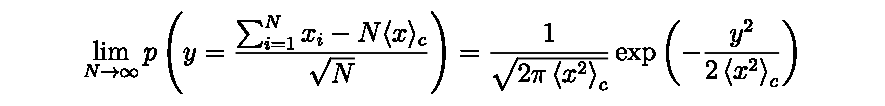

```mathematica
MaTeX["\\lim _{N \\rightarrow \\infty} p\\left(y=\\frac{\\sum_{i=1}^{N} x_{i}-N\\langle x\\rangle_{c}}{\\sqrt{N}}\\right)=\\frac{1}{\\sqrt{2 \\pi\\left\\langle x^{2}\\right\\rangle_{c}}} \\exp \\left(-\\frac{y^{2}}{2\\left\\langle x^{2}\\right\\rangle_{c}}\\right)", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\lim _{N \\rightarrow \\infty} p\\left(y=\\frac{\\sum_{i=1}^{N} x_{i}-N\\langle x\\rangle_{c}}{\\sqrt{N}}\\right)=\\frac{1}{\\sqrt{2 \\pi\\left\\langle x^{2}\\right\\rangle_{c}}} \\exp \\left(-\\frac{y^{2}}{2\\left\\langle x^{2}\\right\\rangle_{c}}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

lim_(N→∞) p[y==(∑_(i=1)^N x_i-N ⟨x⟩_c)/(√N)]==(ⅇ^(-y^2/(2 ⟨x^2⟩_c)))/(√(2 π ⟨x^2⟩_c))

```mathematica
(42) -- (Note that the Gaussian distribution is the only distribution with only first and second cumulants.)
```

(43) -- The convergence of the PDF for the sum of many random variables to a normal distribution is a most important result in the context of statistical mechanics where such sums are frequently encountered. The central limit theorem states a more general form of this result: It is not necessary for the random variables to be independent, as the condition,

```mathematica
MaTeX["\\sum_{i_{1}, \\cdots, i_{m}}^{N}\\left\\langle x_{i_{1}} \\cdots x_{i_{m}}\\right\\rangle_{c} \\ll \mathcal{O}\\left(N^{m / 2}\\right)",Magnification->5]
```

-Graphics-

is sufficient for the validity of eq.(II.49)

## II.F Rules for Large Numbers

```mathematica
(44) -- Today, we're going to talk about something really cool called "Rules for Large Numbers." You see, when we have a lot of tiny things like atoms or molecules in a big object, they follow some special rules. These rules make it easier for us to understand how the whole object behaves.

First, when we have a really, really big number of these tiny things, they start to behave in a more predictable way. It's like having a huge group of friends – you can guess how they'll act as a group, even if each person is different.

Second, when we look at the whole object, we don't need to worry about every single tiny thing inside it. We can focus on the overall behavior, which makes things much simpler.

Finally, these rules help us understand how big objects like planets or stars work. They also help us understand important things like how hot or cold something is, or how much energy it has.

So, remember, when you have a lot of tiny things, they follow these special "Rules for Large Numbers," which make it easier for us to understand the big picture!
```

```mathematica
(45) -- There are typically three types of N dependence encountered in the thermodynamic limit:
```

## (a) Intensive quantities

(46) -- (a) Intensive quantities, such as temperature $T$, and generalized forces, e.g. pressure $P$, and magnetic field $\vec{B}$, are independent of $N$, i.e. $\mathcal{O}\left(N^{0}\right)$.

(46) -- Imagine you have a bunch of toys, like cars, dolls, or blocks. Some things about these toys don't change no matter how many toys you have. For example, the color of a toy car doesn't change if you have one car or ten cars. The color is the same.

In the same way, there are some things in the world of heat and energy that don't change even if you have a lot of stuff or just a little bit of stuff. These things are called "intensive quantities."

Temperature is one of these intensive quantities. It's like the color of your toys. If you have one toy car or ten toy cars, the color doesn't change. In the same way, if you have a little bit of hot water or a lot of hot water, the temperature stays the same.

Pressure and magnetic field are also intensive quantities. They are like the color of your toys. They don't change no matter how much stuff you have.

So, when we talk about intensive quantities like temperature, pressure, and magnetic field, we don't need to worry about how much stuff we have. These quantities stay the same whether we have a little bit or a lot.

## (b) Extensive quantities

```mathematica
(47) -- (b) Extensive quantities, such as energy $E$, entropy $S$, and generalized displacements, e.g. volume $V$, and magnetization $\vec{M}$, are proportional to $N$, i.e. $\mathcal{O}\left(N^{1}\right)$.

(47) -- Little one, let's imagine a big family with lots of people. The more people there are, the more food they need to eat, right? That's because the amount of food needed grows with the number of people.

Similarly, in the world of tiny particles like atoms and molecules, there are things like energy, entropy, volume, and magnetization. These things also grow bigger when there are more particles.

For example, if you have a lot of atoms in a gas, the total energy of the gas will be higher than if you only had a few atoms. The same goes for entropy, which is like a measure of disorder, and volume, which is the amount of space the gas takes up.

Just like how a big family needs more food than a small family, a bunch of atoms or molecules need more energy, entropy, and volume than just a few of them.
```

## (c) Exponential dependence

(48) -- (c) Exponential dependence, i.e.,

```mathematica
MaTeX["\\mathcal{O}(\\exp (N \\phi))", Magnification->6]
```

-Graphics-

is encountered in enumerating discrete micro-states, or computing available volumes in phase space.

(48) -- When we count all the tiny ways things can be arranged, or look at all the possible spaces they can fit into, we often find that the number gets really, really big really fast! It grows faster than just adding more each time. Instead, it multiplies itself over and over again, getting huger and huger!

This super-fast growing pattern happens a lot when we study how things like atoms or molecules can rearrange themselves in different setups. The more things we have, the more mind-bogglingly huge the number of possibilities becomes. It's like each new thing we add lets the possibilities explode!

(49) -- Other asymptotic dependencies are certainly not ruled out a priori. For example, the Coulomb energy of $N$ ions at fixed density scales as $Q^{2} / R \sim N^{5 / 3}$. Such dependencies are rarely encountered in every day physics. The Coulomb interaction of ions is quickly\\
screened by counter-ions, resulting in an extensive overall energy. (This is not the case in astrophysical problems since the gravitational energy can not be screened. For example the entropy of a black hole is proportional to the square of its mass.)

(49) -- In our world, we sometimes see things that don't follow the usual rules. For example, imagine you have a bunch of tiny, tiny balls that don't like each other. If you put them all together, their energy grows differently than usual. Instead of growing like the number of balls, it grows like the number of balls raised to the power of 5/3.

This kind of behavior is not something we see every day. Usually, when we have things that don't like each other, like the tiny balls and their opposites, their energy grows just like the number of things we have.

But in some special places, like in space with big stars and black holes, the energy grows differently. The energy of a black hole grows like the square of its size.

So, while we don't usually see these different kinds of energy growth in our everyday life, they can happen in special situations, like with tiny balls that really don't like each other, or with huge things like black holes in space.

```mathematica
(50) -- In statistical mechanics we frequently encounter sums or integrals of exponential variables. Performing such sums in the thermodynamic limit is considerably simplified due to the following results.
```

```mathematica
(51) -- (1) Summation of Exponential Quantities
```

```mathematica
(52) -- Consider the sum
```

Statistical Mechanics
Ramirez (53)

```mathematica
MaTeX["\\mathcal{S}=\\sum_{i=1}^{\\mathcal{N}} \\mathcal{E}_{i}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\mathcal{S}=\\sum_{i=1}^{\\mathcal{N}} \\mathcal{(Ener)}_{i}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S==∑_(i=1)^N Ener_i

```mathematica
(54) -- where each term is positive, with an exponential dependence on N,
```

Statistical Mechanics
Ramirez (55)

```mathematica
MaTeX["0 \\leq \\mathcal{E}_{i} \\sim \\mathcal{O}\\left(\\exp \\left(N \\phi_{i}\\right)\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["0 \\leq \\mathcal{(Ener)}_{i} \\sim \\mathcal{O}\\left(\\exp \\left((Num) \\phi_{i}\\right)\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(0≤Ener_i)∼O[ⅇ^(Num ϕ_i)]

```mathematica
(56) -- and the number of terms N, is proportional to some power of N. Such a sum can be approximated by its largest term $\mathcal{E}_{\max }$, in the following sense. Since for each term in the $\operatorname{sum}, 0 \leq \mathcal{E}_{i} \leq \mathcal{E}_{\text {max }}$,

(56) -- Imagine you have a big bag filled with lots and lots of toys. In this bag, there are N different kinds of toys. Now, you want to count how many toys you have in total. To do this, you need to count the number of toys for each kind and then add them all up. This is like the sum we are talking about.

But, there's a trick! Instead of counting every single toy, we can just look at the kind of toy that has the most toys. Let's call this the "biggest group" of toys, and let's say there are E_max toys in this biggest group.

Now, since no group can have more toys than the biggest group, we know that every other group must have fewer toys than E_max. So, if we just count the toys in the biggest group, we will have a good idea of how many toys are in the whole bag!

The number of different ways to arrange the toys in the bag is like the N different kinds of toys we have. And the sum we are talking about is like counting all the toys by looking at each group and adding them up. But instead of doing that, we can just look at the biggest group, E_max, and that will give us a pretty good idea of how many toys are in the whole bag.
```

Statistical Mechanics
Ramirez (57)

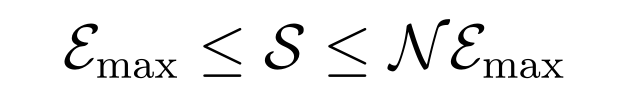

```mathematica
MaTeX["\\mathcal{E}_{\\max} \\leq \\mathcal{S} \\leq \\mathcal{N} \\mathcal{E}_{\\max}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\mathcal{(Ener)}_{\\max} \\leq \\mathcal{S} \\leq \\mathcal{(Num)} \\mathcal{(Ener)}_{\\max}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Ener_max≤S≤Num Ener_max

(58) -- An intensive quantity can be constructed from ln(S)/N, which is bounded by

Statistical Mechanics
Ramirez (59)

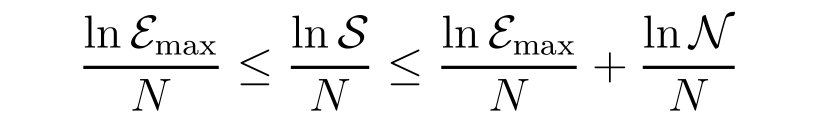

```mathematica
MaTeX["\\frac{\\ln \\mathcal{E}_{\\max}}{N} \\leq \\frac{\\ln \\mathcal{S}}{N} \\leq \\frac{\\ln \\mathcal{E}_{\\max}}{N}+\\frac{\\ln \\mathcal{N}}{N}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\frac{\\ln \\mathcal{(Ener)}_{\\max}}{Num} \\leq \\frac{\\ln \\mathcal{S}}{Num} \\leq \\frac{\\ln \\mathcal{(Ener)}_{\\max}}{Num}+\\frac{\\ln \\mathcal{(Num)}}{Num}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(ln Ener_max)/Num≤(ln S)/Num≤(ln Ener_max)/Num+Log[Num]/Num

```mathematica
(60) -- For $\mathcal{N} \propto N^{p}$, the ratio ln(N) / N vanishes in the large N limit, and
```

Statistical Mechanics
Ramirez (61)

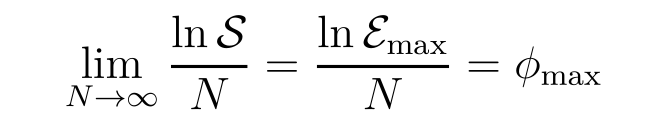

```mathematica
MaTeX["\\lim _{N \\rightarrow \\infty} \\frac{\\ln \\mathcal{S}}{N}=\\frac{\\ln \\mathcal{E}_{\\max}}{N}=\\phi_{\\max}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\lim _{(Num) \\rightarrow \\infty} \\frac{\\ln \\mathcal{S}}{Num}=\\frac{\\ln \\mathcal{(Ener)}_{\\max}}{Num}=\\phi_{\\max}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

lim_(Num→∞) (ln S)/Num==(ln Ener_max)/Num==ϕ_max

(62) -- (2) Saddle Point Integration

(62) -- (2) Saddle Point Integration

Imagine you're on a swing, going up and down. The highest point where you stop for a moment before coming back down is called the "saddle point." In our world, there are many tiny particles like atoms and molecules, and they all move around in different ways. Sometimes, they can reach a special "saddle point" where they pause for a tiny moment before continuing their journey.

We can use special math tricks, called "saddle point integration," to understand how these particles behave when they reach these special "saddle points." By doing this, we can learn more about the world around us and how everything works together.

Just like you need to understand the swing's motion to play on it correctly, we need to understand the particles' movements to figure out many important things in our world. And "saddle point integration" helps us do that in a very clever way!

```mathematica
(63) -- Similarly, an integral of the form
```

Statistical Mechanics
Ramirez (64)

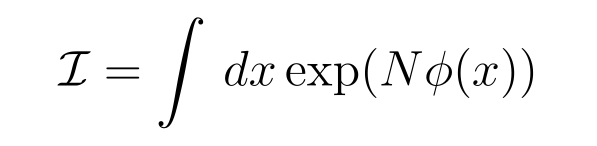

```mathematica
MaTeX["\\mathcal{I}=\\int \\, d x \\exp (N \\phi(x))", Magnification -> 4]
```

(65) -- can be approximated by the maximum value of the integrand, obtained at a point $x_{\max }$ which maximizes the exponent $\phi(x)$. Expanding around this point,

Statistical Mechanics
Ramirez (66)

```mathematica
MaTeX["\\mathcal{I}=\\int d x \\exp \\left\\{N\\left[\\phi\\left(x_{\\max}\\right)-\\frac{1}{2}\\left|\\phi^{\\prime \\prime}\\left(x_{\\max}\\right)\\right|\\left(x-x_{\\max}\\right)^{2}+\\cdots\\right]\\right\\}", Magnification -> 4]
```

-Graphics-

(67) -- Note that at the maximum, the first derivative $\phi^{\prime}\left(x_{\max }\right)$, is zero, while the second derivative $\phi^{\prime \prime}\left(x_{\max }\right)$, is negative. Terminating the series at the quadratic order results in

(67) -- Once upon a time, there was a special number called φ(x). It had a secret hiding place where it was the biggest, called x_max. At this hiding place, if you looked carefully, you would notice two things.

First, if you tried to make φ(x) any bigger or smaller, it wouldn't change at all. It was like φ(x) was perfectly happy and didn't want to move from its special spot.

Second, if you looked even more closely, you would see that φ(x) was a little bit squished down at its hiding place. It wasn't completely flat, but it had a tiny curve that made it look a little bit like a frown.

Now, when we tried to describe φ(x) using only its special hiding place and the tiny frown, we ended up with a simpler version of φ(x) that looked like a curve made up of two parts: a straight line and a little dip. This simpler version was a good friend of φ(x), and it helped us understand what φ(x) was really like, even though it wasn't exactly the same.

Statistical Mechanics
Ramirez (68)

```mathematica
MaTeX["\\mathcal{I} \\approx e^{N \\phi\\left(x_{\\max}\\right)} \\int  \\exp \\left[-\\frac{N}{2}\\left|\\phi^{\\prime \\prime}\\left(x_{\\max}\\right)\\right|\\left(x-x_{\\max}\\right)^{2}\\right] \\approx \\sqrt{\\frac{2 \\pi}{N\\left|\\phi^{\\prime \\prime}\\left(x_{\\max}\\right)\\right|}} e^{N \\phi\\left(x_{\\max}\\right)}\\,  d x", Magnification -> 4]
```

-Graphics-

```mathematica
(69) -- where the range of integration has been extended to $[-\infty, \infty]$. The latter is justified since the integrand is negligibly small outside the neighborhood of $x_{\max }$.

(69) -- When we look at how things move and change in the world, we sometimes need to study a special area called "Thermodynamics and Mechanical Statistics." It's like solving a puzzle, but with numbers and shapes.

In this part of the puzzle, we're looking at how things move and change in a special way. We want to see what happens when we make the puzzle bigger and bigger, like stretching a rubber band.

Imagine you have a rubber band that you can stretch as far as you want. When you stretch it a little bit, it's easy to see what's happening. But what if you stretch it really, really far? So far that it's almost like it's stretching to infinity?

That's what we're doing here. We're making our puzzle so big that it's like it's stretching to infinity. But even though it's super big, we can still solve it because the important parts are still happening in the middle, where we can see them.

It's like having a really long rubber band, but the part you care about is still in the middle. The rest of the rubber band is so far away that it doesn't really matter.

So, we're making our puzzle really big, but we're still focusing on the important part in the middle. That way, we can solve the puzzle and learn more about how things move and change in the world.
```

```mathematica
(70) -- There are two kinds of fixes for the result we just found. First, there are some extra terms that come after the main term when we expand phi(x) around x_max. These extra terms can be treated as small corrections, and they form a series where each term gets smaller and smaller as N gets bigger. 

Secondly, there may be other places where phi(x) has a local maximum, let's call one of those places x_max'. If we find such a place, we can do a similar calculation to the one we did for x_max, and add that result to our original result. However, these extra contributions are much smaller than the main result, by a factor that gets smaller and smaller as N gets bigger. 

Since all these corrections become negligible when N is very large, we can ignore them in the thermodynamic limit.
```

Statistical Mechanics
Ramirez (71)

```mathematica
MaTeX["\\lim _{N \\rightarrow \\infty} \\frac{\\ln \\mathcal{I}}{N}=\\lim _{N \\rightarrow \\infty}\\left[\\phi\\left(x_{\\max}\\right)-\\frac{1}{2 N} \\ln \\left(\\frac{N\\left|\\phi^{\\prime \\prime}\\left(x_{\\max}\\right)\\right|}{2 \\pi}\\right)+\\mathcal{O}\\left(\\frac{1}{N^{2}}\\right)\\right]=\\phi\\left(x_{\\max}\\right)", Magnification -> 4]
```

-Graphics-

(72) -- The saddle point method for evaluating integrals is the extension of the above result to more general integrands, and integration paths in the complex plane. (The appropriate extremum in the complex plane is a saddle point.) The simplified version presented above is sufficient for the purposes of this course.

(72) -- In the big world of numbers and shapes, we sometimes need to find special points called "saddle points." These points help us understand how things move and change, just like how a real saddle helps a rider stay balanced on a horse.

When we look at the shapes and patterns of numbers, sometimes it's like looking at a map with hills and valleys. The saddle points are like the places where the hills and valleys meet, and they help us figure out how to explore the whole map.

In our study of how things move and change, we can use these special saddle points to understand the bigger picture. It's like having a secret key that unlocks the door to a whole new world of understanding.

## Stirling’s approximation for N!

```mathematica
(73) -- Stirling's approximation for N! at large N can be obtained by saddle point integration. In order to get an integral representation of N!, start with the result

(73) -- About counting and estimating things in nature.

Imagine you have a bunch of toys, let's say N toys. You want to arrange them in a line, but there are so many ways to do it! How can we count all the possible arrangements? Well, that's where the magical formula N! comes into play.

N! is a special number that tells you how many different ways you can arrange N things in a line. For example, if you have 3 toys, there are 3! = 6 ways to arrange them.

Now, when you have a lot of toys, like a really big number N, it becomes very hard to calculate N! directly. But don't worry, there's a clever trick called Stirling's approximation that helps us estimate N! without having to count everything one by one.

You see, N! is like a big number that we can represent as an integral, which is like a special kind of sum. And to make it easier to calculate, we use a technique called "saddle point integration." It's like finding a special point in the integral that makes the calculations simpler.

So, even though you might not understand all the details yet, just remember that Stirling's approximation is a clever way to estimate N! when N is really big, and it's based on some cool mathematical ideas called integrals and saddle point integration.
```

Statistical Mechanics
Ramirez (74)

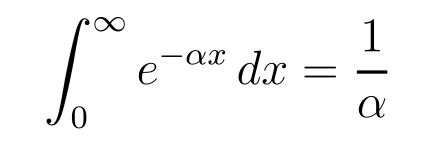

```mathematica
MaTeX["\\int _{0}^{\\infty} e^{-\\alpha x} \\,  d x=\\frac{1}{\\alpha}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\int _{0}^{\\infty} e^{-\\alpha x} \\,  d x=\\frac{1}{\\alpha}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

∫_0^∞ e^(-α x)ⅆx==1/α

(75) -- Repeated differentiation of both sides of the above equation with respect to $\alpha$ leads to

Statistical Mechanics
Ramirez (76)

```mathematica
MaTeX["\\int _{0}^{\\infty} x^{N} e^{-\\alpha x} \\,  d x=\\frac{N!}{\\alpha^{N+1}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\int _{0}^{\\infty} x^{(Num)} e^{-\\alpha x} \\,  d x=\\frac{(Num)!}{\\alpha^{(Num)+1}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

∫_0^∞ x^Num e^(-α x)ⅆx==(Num!)/α^(Num+1)

(77) -- Although the above result only applies to integer N, it is possible to define by analytical continuation a function,

Statistical Mechanics
Ramirez (78)

```mathematica
MaTeX["\\Gamma(N+1) \\equiv N!=\\int _{0}^{\\infty} x^{N} e^{-x}\\,  d x", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\Gamma((Num)+1) \\equiv (Num)!=\\int _{0}^{\\infty} x^{(Num)} e^{-x}\\,  d x",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(Gamma[Num+1]≡Num!)==∫_0^∞ x^Num e^-xⅆx

```mathematica
(79) -- for all N. While the integral in eq.(II.61) is not exactly in the form of eq.(II.55), it can still be evaluated by a similar method. The integrand can be written as $\exp (N \phi(x))$, with $\phi(x)=\ln x-x / N$. The exponent has a maximum at $x_{\max }=N$, with $\phi\left(x_{\max }\right)=\ln N-1$, and $\phi^{\prime \prime}\left(x_{\max }\right)=-1 / N^{2}$. Expanding the integrand in eq.(II.61) around this point yields,


(79) -- Imagine a group of N friends who love to share their favorite treats. Each friend has one treat, and they all put their treats in a big basket. Now, they want to share the treats equally among themselves, but they don't know how many treats each friend will get.

To find out, they need to count how many treats are in the basket. But instead of counting one by one, which can be very tiring, they use a special trick. They look at the equation (II.61), which helps them calculate the total number of treats in the basket without actually counting them.

The equation (II.61) looks complicated, but it's like a secret code that helps them solve the problem. It has a special part called the "integrand," which is like a magic word that describes how the treats are arranged in the basket.

The magic word is "exp (N phi(x))," where "phi(x)" is another secret code that means "ln x - x / N." This code tells them how many treats each friend might get, and it has a special point called "x_max = N" where the number of treats is just right.

At this special point, the code "phi(x_max)" becomes "ln N - 1," which is like a special number that helps them solve the problem. They also need to know another number called "phi''(x_max)," which is "-1 / N^2."

By using these special numbers and the equation (II.61), the friends can find out how many treats are in the basket without counting them one by one. They can then share the treats equally among themselves, and everyone will be happy!
```

## Practice in MMA: enviar libro hoy!

Statistical Mechanics
Ramirez (80)

```mathematica
MaTeX["N!\\approx \\int dx  \\exp \\left(N \\ln N-N-\\frac{1}{2 N}(x-N)^{2}\\right) \\approx N^{N} e^{-N} \\sqrt{2 \\pi N}", Magnification -> 4]
```

-Graphics-

(81) -- Imagine you have a bunch of toys, and you want to count how many different ways you can arrange them. That's what this text is all about!

You see, there's a special way to count the toys called the "Stirling formula." It's like a magic trick that helps you count really, really big numbers of toys.

Now, when you're counting toys, sometimes you have to look at them from really far away, and sometimes you have to look at them from really close up. The text talks about how to do that.

It says that when you're looking at the toys from really far away, you can use a special trick called "extending the limits to negative infinity and positive infinity." That means you're looking at the toys from so far away that you can't even see the edges of the room they're in!

And when you're looking at the toys from really close up, you can use the "Stirling formula" to count them. It's like a special code that helps you count the toys faster and easier.

The text is all about how to use these tricks to count toys in different ways. It's like a secret code that only the really smart toy-counters know about!

Statistical Mechanics
Ramirez (82)

```mathematica
MaTeX["\\ln N!=N \\ln N-N+\\frac{1}{2} \\ln (2 \\pi N)+\\mathcal{O}\\left(\\frac{1}{N}\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\ln (Num)!=(Num) \\ln (Num)-(Num)+\\frac{1}{2} \\ln (2 \\pi (Num))+\\mathcal{O}\\left(\\frac{1}{(Num)}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

Log[Num]!==Num Log[Num]-Num+1/2 Log[2 π[Num]]+O[1/Num]

## II.G Information, Entropy, and Estimation

### Information

(83) -- Information: Consider a random variable with a discrete set of outcomes $\mathcal{S}=\left\{x_{i}\right\}$, occurring with probabilities $\{p(i)\}$, for $i=1, \cdots, M$. In the context of information theory, there is a precise meaning to the information content of a probability distribution: Let us construct a message from $N$ independent outcomes of the random variable. Since there are $M$ possibilities for each character in this message, it has an apparent information content of $N \ln _{2} M$ bits; i.e. this many binary bits of information have to be transmitted to convey the message precisely. On the other hand, the probabilities $\{p(i)\}$ limit the types of messages that are likely. For example, if $p_{2} \gg p_{1}$, it is very unlikely to construct a message with more $x_{1}$ than $x_{2}$. In particular, in the limit of large $N$, we expect the message to contain "roughly" $\left\{N_{i}=N p_{i}\right\}$ occurrences of each symbol. ${ }^{\dagger}$ The number of typical messages thus corresponds to the number of ways of rearranging the $\left\{N_{i}\right\}$ occurrences of $\left\{x_{i}\right\}$, and is given by the multinomial coefficient



(83) -- Let us tell you a story about a game we play with letters and numbers.

Imagine we have a bag full of different colored balls, and each color has its own special number. We can pull out balls from the bag one by one and write down the numbers on a piece of paper. The more balls of a certain color we have in the bag, the more likely we are to pull out that color's number.

Now, let's say we want to send a secret message to a friend using these numbers. The longer the message, the more numbers we need to write down. But here's the fun part: if we know how many balls of each color are in the bag, we can guess what numbers will appear most often in our message!

For example, if there are lots of red balls in the bag, we can expect to see the red ball's number many times in our message. And if there are only a few blue balls, the blue ball's number won't appear as often.

But how do we know how many different ways we can arrange these numbers in our message? Well, we can use a special trick called the "multinomial coefficient" to figure that out. It's like counting how many different ways we can line up the balls in a row, with each color in its own group.

So, you see, by playing this game with letters and numbers, we can learn about how to send secret messages and understand how likely different numbers are to appear. Isn't that exciting?

Statistical Mechanics
Ramirez (84)

## Multinomial Coefficient

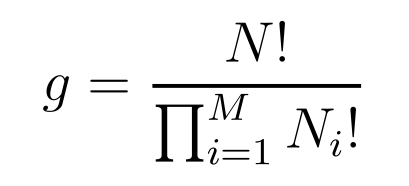

```mathematica
MaTeX["g=\\frac{N!}{\\prod_{i=1}^{M} N_{i}!}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["g=\\frac{(Num)!}{\\prod_{i=1}^{M} (Num)_{i}!}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

g==(Num!)/(∏_(i=1)^M Num_i!)

```mathematica
(85) -- This is much smaller than the total number of messages $M^{n}$. To specify one out of $g$ possible sequences requires

(85) -- Once upon a time, there was a magical world where tiny, tiny particles called molecules danced around in a special way. These molecules loved to play games, and one of their favorite games was called "Message Passing."

In this game, the molecules would line up in a long row, and each molecule would whisper a special message to its neighbor. The messages could be anything, like "I'm a happy molecule!" or "Let's dance a jig!"

Now, in this magical world, there were lots and lots of molecules, and they could line up in many different ways. In fact, there were so many different ways to line up that it would be impossible to count them all!

But here's the thing: even though there were so many different ways for the molecules to line up, not all of those ways were equally fun or interesting. Some ways were really boring, with all the molecules whispering the same message over and over again. Other ways were much more exciting, with each molecule whispering a different message to its neighbor.

The molecules had a special word for these exciting ways of lining up. They called them "sequences." And they knew that out of all the different ways they could line up, only a few of those ways were really special sequences.

So, when the molecules wanted to play their "Message Passing" game, they had to figure out a way to choose one of those special sequences. And to do that, they had to use a special kind of magic called "specifying."

Specifying was like giving the molecules a set of instructions, telling them exactly how to line up and what messages to whisper. And the more instructions they had, the easier it was to choose one of those special sequences.

But here's the really cool part: even though there were so many different ways for the molecules to line up, the molecules didn't need a whole lot of instructions to choose one of the special sequences. They just needed a few simple rules, and they could create all kinds of exciting and interesting messages!

And that's why the molecules loved playing their "Message Passing" game so much. It was like a magical puzzle, where they had to use their clever minds to figure out the best way to line up and whisper their messages. And every time they played, they learned something new and exciting about the world around them.
```

Statistical Mechanics
Ramirez (86)

```mathematica
MaTeX["\\ln _{2} g \\approx-N \\sum_{i=1}^{M} p_{i} \\ln _{2} p_{i} \\quad(\\text {for} N \\rightarrow \\infty)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\ln _{2} g \\approx-N \\sum_{i=1}^{M} p_{i} \\ln _{2} p_{i} \\quad(\\text {for} (Num) \\rightarrow \\infty)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ln_2 g≈-N ∑_(i=1)^M p_i ln_2 p_i (for[Num]→∞)

```mathematica
(87) -- $\dagger$ More precisely, the probability of finding any $N_{i}$ that is different from $N p_{i}$ by more than $\pm \sqrt{N}$ becomes exponentially small in $N$, as $N \rightarrow \infty$.\\
bits of information. The last result is obtained by applying Stirling's approximation for $\ln N$ !. It can also be obtained by noting that
```

Statistical Mechanics
Ramirez (88)

```mathematica
MaTeX["1=\\left(\\sum_{i} p_{i}\\right)^{N}=\\sum_{\\left\\{N_{i}\\right\\}} N!\\prod_{i=1}^{M} \\frac{p_{i}^{N_{i}}}{N_{i}!} \\approx g \\prod_{i=1}^{M} p_{i}^{N p_{i}}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["1=\\left(\\sum_{i} p_{i}\\right)^{N}=\\sum_{\\left\\{N_{i}\\right\\}} N!\\prod_{i=1}^{M} \\frac{p_{i}^{N_{i}}}{N_{i}!} \\approx g \\prod_{i=1}^{M} p_{i}^{N p_{i}}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(1==(∑_i p_i)^N==Sum[N! ∏_(i=1)^M p_i^N_i/(N_i!),{N_i}])≈g ∏_(i=1)^M p_i^(N p_i)

```mathematica
(89) -- where the sum has been replaced by its largest term, as justified in the previous section.
```

## Shannon’s Theorem

(90) -- Shannon's Theorem proves more rigorously that the minimum number of bits necessary to ensure that the percentage of errors in $N$ trials vanishes in the $N \rightarrow \infty$ limit, is $\ln _{2} g$. For any non-uniform distribution, this is less than the $N \ln _{2} M$ bits needed in the absence of any information on relative probabilities. The difference per trial is thus attributed to the information content of the probability distribution, and is given by


(90) -- Once upon a time, there was a clever scientist named Shannon who discovered something amazing about numbers and mistakes. Imagine you have a bunch of toys, and you want to tell your friend which ones you have without making any mistakes. The more toys you have, the harder it becomes to do this without getting mixed up.

Shannon found a special way to figure out the smallest number of pieces of information (like saying "red ball" or "green car") you need to share with your friend so that they can guess your toys perfectly, even if you have a lot of them. This number is called ln2g, and it's like a magic key that unlocks the door to understanding how to share information without making mistakes.

Here's the cool part: Shannon showed that if you use this magic key, you'll need fewer pieces of information than if you just tried to list all your toys one by one (which would be a really long list!). The difference between these two numbers is like a secret code that tells you how special your toy collection is. The more different kinds of toys you have, the more special your collection becomes, and the more this secret code helps you share information about it without getting mixed up.

So, next time you want to tell your friend about your toys, remember Shannon's magic key, ln2g, and the secret code that makes your collection extra special!

Statistical Mechanics
Ramirez (91)

```mathematica
MaTeX["I\\left[\\left\\{p_{i}\\right\\}\\right]=\\ln _{2} M+\\sum_{i=1}^{M} p_{i} \\ln _{2} p_{i}", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["I\\left[\\left\\{p_{i}\\right\\}\\right]=\\ln _{2} M+\\sum_{i=1}^{M} p_{i} \\ln _{2} p_{i}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ⅈ[{p_i}]==ln_2 M+∑_(i=1)^M p_i ln_2 p_i

## Entropy:

```mathematica
(92) -- Entropy: Eq.(II.64) is encountered frequently in statistical mechanics in the context of mixing M distinct components; its natural logarithm is related to the entropy of mixing. More generally, we can define an entropy for any probability distribution as


(92) -- You know how sometimes you have a box of different colored candies, and you like to mix them all together? Well, entropy is like measuring how mixed up or disordered the candies are in the box. The more mixed up they are, the higher the entropy.

Now, imagine you have a special box with different kinds of candies, like chocolates, gummies, and lollipops. We can use a special number called "entropy" to tell us how mixed up or disordered these different kinds of candies are in the box.

The entropy number is like a secret code that helps us understand how mixed up or disordered things are. The higher the entropy number, the more mixed up or disordered the candies are in the box.

So, whenever you see different things mixed together, like different kinds of candies in a box, you can use entropy to measure how mixed up or disordered they are. Pretty cool, right?
```

Statistical Mechanics
Ramirez (93)

```mathematica
MaTeX["S=-\\sum_{i=1}^{M} p(i) \\ln p(i)=-\\langle\\ln p(i)\\rangle", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["S=-\\sum_{i=1}^{M} p(i) \\ln p(i)=-\\langle\\ln p(i)\\rangle",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S==-∑_(i=1)^M p[i] ln p[i]==-⟨ln p[i]⟩

(94) -- The above entropy takes a minimum value of zero for the delta-function distribution $p(i)=\delta_{i, j}$, and a maximum value of $\ln M$ for the uniform distribution, $p(i)=1 / M . S$ is thus a measure of dispersity (disorder) of the distribution, and does not depend on the values of the random variables $\left\{x_{i}\right\}$. A one to one mapping to $f_{i}=F\left(x_{i}\right)$ leaves the entropy unchanged, while a many to one mapping makes the distribution more ordered and decrease $S$. For example, if the two values, $x_{1}$ and $x_{2}$, are mapped onto the same $f$, the change in entropy is


(94) -- Imagine you have a bag of marbles. Each marble is a different color. If you have only one marble in the bag, it's easy to know which color it is. But if you have many marbles of different colors, it gets harder to guess which color you'll pick next.

The more different colors of marbles you have in the bag, the more mixed up or disordered the bag is. We call this disorder "entropy." If you have only one color of marble, the entropy is zero because everything is in order. But if you have many different colors, the entropy is high because it's all mixed up.

Entropy is like a measure of how mixed up or disordered things are. It doesn't depend on what the actual colors are, just on how many different colors you have. If you take two different colored marbles and paint them the same color, you've made the bag more ordered, so the entropy goes down.

Statistical Mechanics
Ramirez (95)

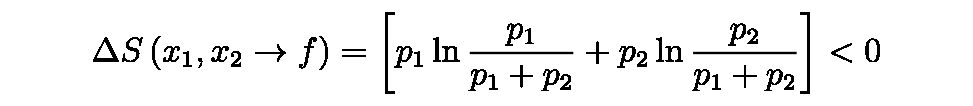

```mathematica
MaTeX["\\Delta S\\left(x_{1}, x_{2} \\rightarrow f\\right)=\\left[p_{1} \\ln \\frac{p_{1}}{p_{1}+p_{2}}+p_{2} \\ln \\frac{p_{2}}{p_{1}+p_{2}}\\right]<0", Magnification -> 4]
```

## Estimation:

```mathematica
(96) --  Estimation: The entropy S, can also be used to quantify subjective estimates of probabilities. In the absence of any information, the best unbiased estimate is that all $M$ outcomes are equally likely. This is the distribution of maximum entropy. If additional information is available, the unbiased estimate is obtained by maximizing the entropy subject to the\\
constraints imposed by this information. For example, if it is known that $\langle F(x)\rangle=f$, we can maximize


(96) -- Today, we're going to talk about a special number called "entropy." It's like a secret code that tells us how mixed up or disorganized things are.

Imagine you have a bunch of toys in a box, and you can't see what's inside. If someone tells you that all the toys are different, like a ball, a car, a doll, and a teddy bear, then the entropy is high. That means there's a lot of variety and everything is all mixed up.

But what if someone says that all the toys in the box are the same, like four teddy bears? In that case, the entropy is low because everything is organized and the same.

Now, let's say you have a magic box that can change the toys inside without you looking. If you don't know anything about what's in the box, the best guess is that all the toys are different. That's the highest entropy, where everything is mixed up.

However, if someone tells you a clue, like "there's at least one ball in the box," then you can make a better guess. You can try to find the most mixed up way of putting toys in the box while still following the clue.

In our special language, we call this "maximizing the entropy subject to constraints." It's like finding the most disorganized way of arranging things while still following the rules.

So, remember, entropy is all about how mixed up or disorganized things are. The higher the entropy, the more variety and messiness there is!
```

Statistical Mechanics
Ramirez (97)

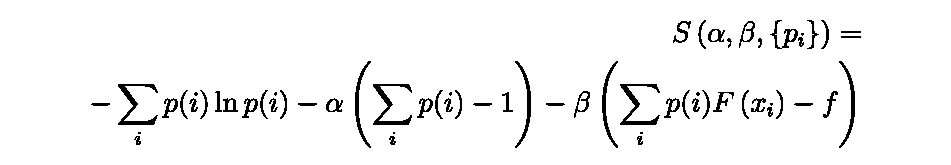

```mathematica
MaTeX["\\begin{aligned} S\\left(\\alpha, \\beta,\\left\\{p_{i}\\right\\}\\right)= \\\\ -\\sum_{i} p(i) \\ln p(i)-\\alpha\\left(\\sum_{i} p(i)-1\\right)-\\beta\\left(\\sum_{i} p(i) F\\left(x_{i}\\right)-f\\right) \\end{aligned}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["S\\left(\\alpha, \\beta,\\left\\{p_{i}\\right\\}\\right)=-\\sum_{i} p(i) \\ln p(i)-\\alpha\\left(\\sum_{i} p(i)-1\\right)-\\beta\\left(\\sum_{i} p(i) F\\left(x_{i}\\right)-f\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

S[α,β,{p_i}]==-∑_i p[i] ln p[i]-α[∑_i p[i]-1]-β[∑_i p[i] F[x_i]-f]

(98) -- where the Lagrange multipliers $\alpha$ and $\beta$ are introduced to impose the constraints of normalization, and $\langle F(x)\rangle=f$, respectively. The result of the optimization is a distribution $p_{i} \propto \exp \left(-\beta F\left(x_{i}\right)\right)$, where the value of $\beta$ is fixed by the constraint. This process can be generalized to an arbitrary number of conditions. It is easy to see that if the first $n$ moments (and hence $n$ cumulants) of a distribution are specified, the unbiased estimate is the exponential of an $n^{\text {th }}$ order polynomial.

(98) -- Once upon a time, there was a curious little scientist named Emily who loved to explore the world of tiny particles and their energies. One day, Emily's teacher introduced her to a special game called "Lagrange Multipliers."

In this game, Emily had to find the perfect distribution of particles, making sure they followed two important rules: first, the total number of particles had to be just right, and second, the average energy of the particles had to match a specific value.

To help her with this task, Emily had two special helpers: alpha and beta. Alpha made sure that the total number of particles was correct, while beta kept track of the average energy.

Emily started by giving each particle a special tag called an "exponential," which depended on its energy and beta. Particles with lower energies got bigger tags, while those with higher energies got smaller ones.

Once all the particles had their tags, Emily adjusted the value of beta until the average of all the tags matched the desired energy value. This way, she could find the perfect distribution of particles that followed both rules.

Emily's teacher explained that this game could be played with even more rules, by adding more helpers like alpha and beta. And the best part? If Emily knew the first few important details about the particles, like their average energy and their total number, she could use a special trick called the "exponential of a polynomial" to find the perfect distribution quickly.

Emily was amazed by this game and couldn't wait to play it again, exploring the fascinating world of particles and their energies.

(99) -- In analogy with eq.(II.68), we can define an entropy for a continuous random variable $\left(\mathcal{S}_{x}=\{-\infty<x<\infty\}\right)$ as

(99) -- Imagine you have a big box filled with lots of little toys. Some toys are big, some are small, some are red, some are blue, and so on. The toys can be anywhere in the box, and they can move around freely.

Now, let's say you want to know how messy or disorganized the toys are inside the box. We can give a number to this messiness, which we call "entropy." The higher the entropy, the more disorganized the toys are.

To find the entropy, we need to look at all the different places the toys can be in the box. If there are many different places where the toys can be, the entropy will be high because the toys can be really messy and scattered all over the box.

But if there are only a few places where the toys can be, the entropy will be low because the toys will be more organized and clustered together.

So, when we talk about entropy, we're talking about how messy or disorganized things are in a system, like the toys in the box. The more places things can be, the higher the entropy, and the more disorganized the system is.

Statistical Mechanics
Ramirez (100)

```mathematica
MaTeX["S=-\\int \\, d x p(x) \\ln p(x)=-\\langle\\ln p(x)\\rangle", Magnification -> 4]
```

-Graphics-

```mathematica
(101) -- There are, however, problems with this definition, as for example S is not invariant under a one to one mapping. (After a change of variable to f=F(x), the entropy is changed by ):
```

```mathematica
MaTeX["\\left\\langle\\left|F^{\\prime}(x)\\right|\\right\\rangle",Magnification->6]
```

-Graphics-

```mathematica
Since the Jacobian of a canonical transformation is unity, canonically conjugate pairs offer a suitable choice of coordinates in classical statistical mechanics. The ambiguities are also removed if the continuous variable is discretized. This happens quite naturally in quantum statistical mechanics where it is usually possible to work with a discrete ladder of states. The appropriate volume for discretization of phase space is set by Planck's constant $\hbar$.
```

## Reference

https://assets.cambridge.org/97805218/73420/frontmatter/9780521873420_frontmatter.pdf

### All old notes:

https://drive.google.com/drive/u/0/folders/1pmmshVrJGU_j6wwc6zTNCo_CQAz9SJmD

```mathematica
ThermoLecsDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"ThermoLecs24/"<>ThermoLecsDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear

```mathematica
nbmmaitexslides=EvaluationNotebook[]; SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData[All,"Printout"],ShowCellLabel->False],Cell[StyleData["Text","Printout",StyleDefinitions->None],CellMargins->{{0,0},{0,0}},Background->GrayLevel[1]], Cell[StyleData["Input","Printout",StyleDefinitions->None],CellMargins->{{0,0},{0,0}},LinebreakAdjustments->{0.85,2,10,1,1}],Cell[StyleData["Code","Printout",StyleDefinitions->None],CellMargins->{{0,0},{0,0}},Background->GrayLevel[1]],Cell[StyleData["Input","Printout",StyleDefinitions->None],CellMargins->{{0,0},{0,0}},LinebreakAdjustments->{0.85,2,10,1,1}],Cell[StyleData["Output","Printout",StyleDefinitions->None],CellMargins->{{0,0},{0,0}}]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]];
SetOptions[nbmmaitexslides,PrintingOptions->{"FirstPageHeader"->True}];
SetOptions[nbmmaitexslides,PrintingOptions->{"PrintingMargins"->{{1,5},{2,5}},
"PaperOrientation"->"Landscape", "PrintCellBrackets"->False, "PrintMultipleHorizontalPages"->False,
"PageSize"->{1040, 460},
"Magnification"->{1.1, 1.1}},
PrintingStartingPageNumber->1,
PageHeaders->{{Cell[TextData[{CounterBox["Page"]}],"PageNumber"],None,None},{Cell[TextData[{CounterBox["Page"]}],"PageNumber"],None,None}},PageFooters->{{None,None,None},{None,None,None}}];
sideBySide[x_,y_,size_]:=Replace[ToBoxes@Grid[{{Pane[Grid[{{1}},Spacings->0,Alignment->{Left,Top}],ImageSize->size],Pane[Grid[{{2}},Spacings->0,Alignment->{Left,Top}],ImageSize->size]}},Spacings->0,Alignment->{Left,Top}],{{{"1"}}->Map[({#})&,x],{{"2"}}->Map[({#})&,y]},Infinity];
PrintingStyleEnvironment/. Options[EvaluationNotebook[],PrintingStyleEnvironment];
NotebookPrint[nbmmaitexslides,NotebookDirectory[]<>"PrintSlidesLec6_v14.pdf"]
```